```mathematica
enenrgyData=Import[FileNameJoin[{NotebookDirectory[],"data","energyData.csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ;
PhiData=Import[FileNameJoin[{NotebookDirectory[],"data","phis.csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ;
```

```mathematica
Mean/@enenrgyData
```

{92.6081,95.05,105.519,103.636,97.3356,104.961,102.594,94.2339,107.616,113.244,105.968,119.157,108.904,88.1753,114.015,102.581,100.443,110.174,124.032,105.667,90.2759,94.5043,106.478,99.3382,101.704,108.581,111.525,110.973,116.534,96.3435,110.376,108.961,102.091,120.131,117.917,105.547,85.9967,98.7446,110.288,92.946,106.271,107.377,94.7572,99.9169,98.2109,117.82,107.363,124.362,124.562,106.02,115.175,105.678,98.4698,99.8799,115.14,105.374,102.685,105.851,101.915,106.259,119.79,106.153,94.0718,124.787,127.407,123.17,112.109,100.824,115.217,109.241,108.566,115.61,133.746,125.69,113.496,131.844,114.539,106.442,128.136,124.367,109.885,119.471,116.421,112.46,61.1641,51.152,62.6875,78.8302,66.478,48.6691,52.8837,69.6752,79.3962,90.0989,55.5747,100.494,71.0506,52.7019,92.1509,56.633}

```mathematica
Mean/@(Select[#,NumberQ]&/@PhiData)
```

{0.625,0.,0.103959,0.480324,0.1475,0.075375,0.,0.198125,0.,0.349582,0.0772223,0.,0.0625,0.140625,0.182983,0.331771,0.215625,0.075,0.189167,0.,0.354375,0.,0.0765,0.305972,0.075375,0.349582,0.0772223,0.,0.0625,0.14525,0.182983,0.331771,0.305972,0.144375,0.189167,0.,0.25,0.,0.063125,0.063125,0.,0.0625,0.0625,0.0625,0.,0.1575,0.063125,0.078125,0.078125,0.063125,0.0625,0.,0.,0.,0.1575,0.,0.063125,0.063125,0.,0.,0.084514,0.,0.0625,0.172446,0.13102,0.0765178,0.0625,0.0625,0.,0.0625,0.0406943,0.0406943,0.165907,0.21355,0.,0.225,0.0908162,0.13102,0.136771,0.0625,0.178038,0.,0.,0.,0.717593,0.,0.050347,0.619443,0.657717,0.170317,0.,0.231087,0.,0.204132,0.207997,0.,0.173988,0.0916664,0.069236,0.408849}

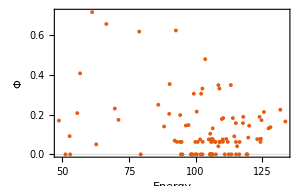

```mathematica
ListPlot[{Mean/@enenrgyData,Mean/@(Select[#,NumberQ]&/@PhiData)}ᵀ,PlotRange->All,PlotTheme->"Scientific",FrameLabel->{"Energy",Φ}]
```

```mathematica
energy2phi={Mean/@enenrgyData,Mean/@(Select[#,NumberQ]&/@PhiData)}ᵀ;
```

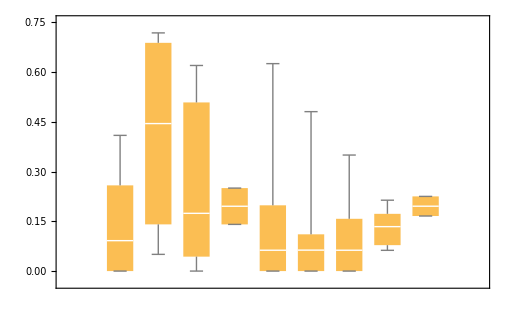

```mathematica
Quiet@BoxWhiskerChart[#ᵀ⟦2⟧&/@Sort[(#⟦1⟧&/@BinLists[energy2phi,{40,150,10},{0,1,1}]),#1⟦1,1⟧<#2⟦1,1⟧&]]
```

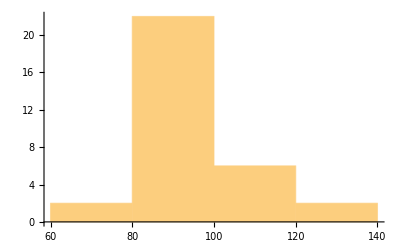
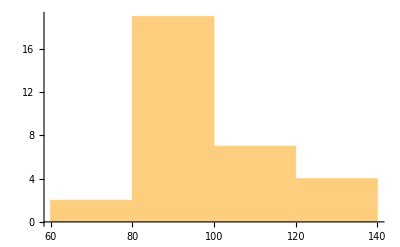
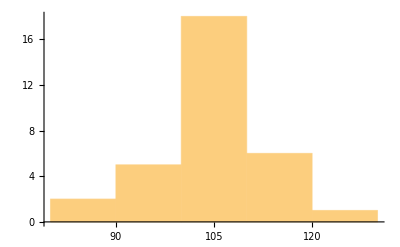
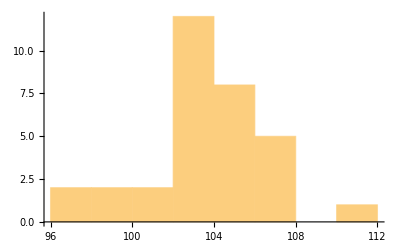
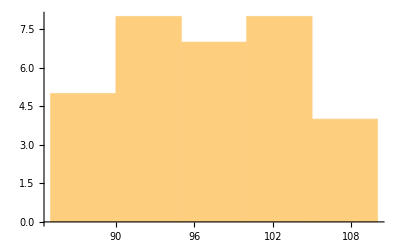

```mathematica
Histogram/@(data⟦1;;5⟧)
```

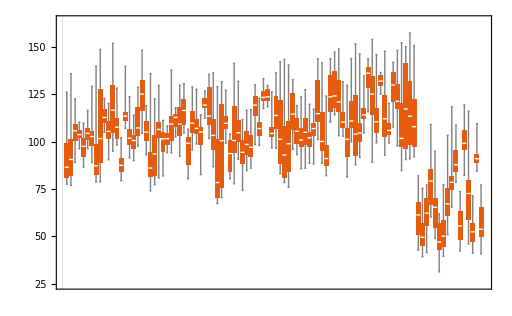

```mathematica
BoxWhiskerChart[data,PerformanceGoal->"Speed",PlotTheme->"Scientific"]
```

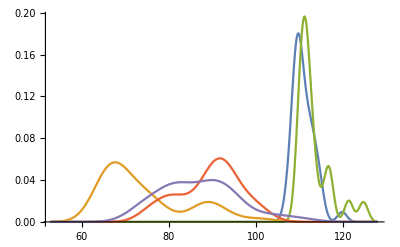

```mathematica
SmoothHistogram[ndata,PlotRange->All]
```